# Figure 2

## Model

```mathematica
sol=DSolve[{A11'[x]==-(1+γ+γo)A11[x]+Ac[x]+α*Ao[x],
Ac'[x]==2γ *A11[x]-(4+2γo/(2+α)+1/3γ)Ac[x]+α*γ*Ao[x]/(2+α),
Ao'[x]==2γo*A11[x]+γo/(2+α)*Ac[x]-(2+2α+γo/(1+2α)+(1+α)/(2+α)γ)Ao[x],
A11[0]==1,Ac[0]==0,Ao[0]==0},{A11,Ac,Ao},x];
```

```mathematica
A11s=(A11[x]/.sol)[[1]];
```

```mathematica
Acs=(Ac[x]/.sol)[[1]];
```

```mathematica
Aos=(Ao[x]/.sol)[[1]];
```

```mathematica
Accs=Acs*γ/6;
```

```mathematica
Aocs=(Acs*γo+Aos*γ)/(2(2+α));
```

```mathematica
Aoos=Aos*γo/(2*(1+2α));
```

```mathematica
A=Simplify[A11s+Acs+Aos+Accs+Aocs+Aoos]
```

-((ⅇ^(-(x (3+γ+2 α (3+γ)+3 γo))/(3+6 α)) (2+5 α+2 α^2) (6+6 α^2+γ+2 α γ+3 α (5+γo)) (-2 (1+2 α) (3+γ+2 α (3+γ)+3 γo)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))+ⅇ^(-1/(6 (2+α) (1+2 α))x (24+12 α^3+5 γ+α (72+14 γ+21 γo)+α^2 (8 γ+6 (9+γo))-3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))) ((1+2 α)^3 γ^4-9 γo (4 α^3-4 (2+γo)+4 α^2 (2+γo)+α (-4+4 γo+γo^2)) (4-4 α^3-α (-6+γo)-2 α^2 (3+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-(1+2 α)^2 γ^3 (-12+8 α^3-4 α^2 (-3+γo)-6 γo-2 α (10+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γ^2 (48+32 α^7+66 γo+9 γo^2+16 α^6 (7+2 γo)+8 α^5 (-13+10 γo+γo^2)-8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+4 α^4 (-135-6 γo+3 γo^2+2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+2 α^3 (-80-82 γo+27 γo^2+8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α^2 (-356-112 γo-49 γo^2+22 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+12 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α (-256-222 γo-30 γo^2+30 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+21 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))+γ (64+128 α^7+240 γo+72 γo^2+224 α^6 (2+γo)+32 α^5 (3+19 γo+4 γo^2)-16 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+26 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+7 γo^2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+8 α^4 (-110-23 γo+30 γo^2+3 γo^3+4 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+8 α^3 (-6 γo^2+3 γo^3+8 (-8+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo (-157+3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))+2 α^2 (21 γo^3+2 γo^2 (-41+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-12 (-14+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-2 γo (62+13 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))-2 α (-9 γo^3+7 γo (-44+5 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+4 (-40+7 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo^2 (-48+19 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))))+ⅇ^(-1/(6 (2+α) (1+2 α))x (24+12 α^3+5 γ+α (72+14 γ+21 γo)+α^2 (8 γ+6 (9+γo))+3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))) ((1+2 α)^3 γ^4+9 γo (4 α^3-4 (2+γo)+4 α^2 (2+γo)+α (-4+4 γo+γo^2)) (-4+4 α^3+α (-6+γo)+2 α^2 (3+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+(1+2 α)^2 γ^3 (12-8 α^3+4 α^2 (-3+γo)+6 γo+2 α (10+γo)+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-γ^2 (-48-32 α^7-66 γo-9 γo^2-16 α^6 (7+2 γo)-8 α^5 (-13+10 γo+γo^2)-8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+4 α^4 (135+6 γo-3 γo^2+2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+2 α^3 (80+82 γo-27 γo^2+8 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+2 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α^2 (356+112 γo+49 γo^2+22 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+12 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-α (256+222 γo+30 γo^2+30 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+21 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))-γ (-64-128 α^7-240 γo-72 γo^2-224 α^6 (2+γo)-32 α^5 (3+19 γo+4 γo^2)-16 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+26 γo √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+7 γo^2 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))+8 α^4 (110+23 γo-30 γo^2-3 γo^3+4 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+8 α^3 (6 γo^2-3 γo^3+8 (8+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo (157+3 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))+2 α^2 (-21 γo^3-12 (14+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+2 γo^2 (41+√((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))-2 γo (-62+13 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))-2 α (9 γo^3+7 γo (44+5 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+4 (40+7 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2))))+γo^2 (48+19 √((1+2 α)^2 (4 α^4+(4+γ)^2+2 α γ (-2+γo)-8 α (2+γo)+4 α^3 (2+γo)+α^2 (-12-4 γ+4 γo+γo^2)))))))))/(2 (2+α) (1+2 α)^2 (96 α^8 (9+2 γ)+(4+γ)^2 (54+21 γ+2 γ^2)+16 α^7 (297+84 γ+4 γ^2+108 γo+18 γ γo)+α (12 γ^4+432 (11+4 γo)+4 γ^3 (55+7 γo)+156 γ (28+9 γo)+γ^2 (1483+353 γo))+8 α^6 (γ^2 (4+8 γo)+6 γ (34+33 γo+3 γo^2)+27 (31+33 γo+6 γo^2))+α^2 (24 γ^4+γ^3 (424+84 γo)+54 (124+24 γo-3 γo^2)+2 γ^2 (1335+469 γo+52 γo^2)+3 γ (2368+930 γo+177 γo^2))-4 α^5 (16 γ^3-4 γ^2 (-69+10 γo+γo^2)-6 γ (-196+66 γo+24 γo^2+γo^3)-27 (-43+51 γo+33 γo^2+4 γo^3))+α^3 (16 γ^4+8 γ^3 (28+9 γo)+4 γ^2 (185+128 γo+33 γo^2)+12 γ (-65-105 γo+24 γo^2+11 γo^3)-27 (172+336 γo+111 γo^2+11 γo^3))+2 α^4 (8 γ^3 (-7+2 γo)+4 γ^2 (-244+20 γo+9 γo^2)+6 γ (-827-168 γo+54 γo^2+5 γo^3)+27 (-284-154 γo+9 γo^2+11 γo^3+γo^4)))))

```mathematica
modelRad=Ai*A/.x->x/lp;
```

```mathematica
modelCTCF=Ai*Aoos/.x->x/lp;
```

## Fig 2cd

```mathematica
hiChipFile = "C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\CTCF_HICHIP.csv";
chiaPetFiles = <|
  "RadGM" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\GMrad21.csv",

  "CTCFK562" -> "C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\k562LoopLengthsCTCF.csv",

  "CTCFGM" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\gm12878LoopLengthsCTCF.csv",

  "CTCFHeLa" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\helaLoopLengthsCTCF.csv"
|>;
```

```mathematica
k562LoopLengths=Rest@Flatten@Import[chiaPetFiles["CTCFK562"],"CSV"]/1000;
gm12878LoopLengths=Rest@Flatten@Import[chiaPetFiles["CTCFGM" ],"CSV"]/1000;
helaLoopLengths=Rest@Flatten@Import[chiaPetFiles["CTCFHeLa"  ],"CSV"]/1000;
GMrad21=Rest@Flatten@Import[chiaPetFiles["RadGM" ],"CSV"]/1000;
```

```mathematica
Min[gm12878LoopLengths]
```

0.008834

```mathematica
hs=HistogramList[Flatten[GMrad21],{20},"PDF"];
```

```mathematica
ft=Table[{hs[[1,i]],N[hs[[2,i]]]},{i,1,Length[hs[[2]]]}];
```

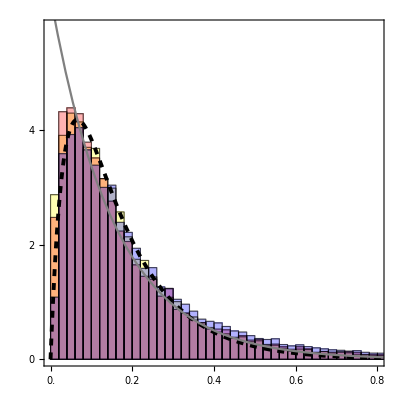

```mathematica
Show[Histogram[{Flatten[k562LoopLengths],Flatten[helaLoopLengths],Flatten[gm12878LoopLengths],Flatten[k562LoopLengths],Flatten[helaLoopLengths],Flatten[gm12878LoopLengths]},{0.02},"PDF",AspectRatio->1,PlotRange->{{0,0.8},{0,5.8}},Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[24],
FrameTicks->{{Range[0,7,2],None},(*left,right*){Range[0,0.8,0.2],None}        (*bottom,top*)},
ChartStyle->{Directive[RGBColor[1,1,0],Opacity[0.3]],Directive[RGBColor[1,0,0],Opacity[0.3]],Directive[RGBColor[0,0,1],Opacity[0.3]],Directive[RGBColor[0,1,0],Opacity[0]],Directive[RGBColor[0.5,0.5,1],Opacity[0]],Directive[RGBColor[1,0.5,0.5],Opacity[0]]}],Plot[{modelCTCF/.Ai->0.0169*1000/.lp->0.431/.α->1.2/.γ->3.1/.γo->4/.x->xi,1/0.158*Exp[-xi/0.158]},{xi,0,0.900},PlotStyle->{Directive[Black,Dashed,Thickness[0.007]],Directive[RGBColor[0.5,0.5,0.5],Thickness[0.004]]}]]
```

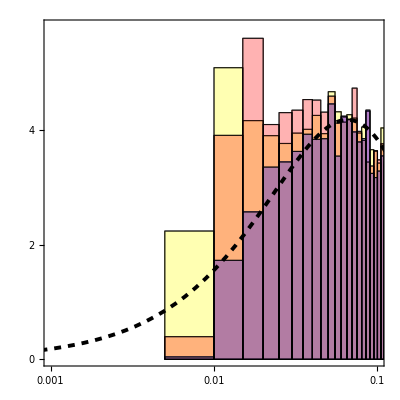

```mathematica
Show[Histogram[{Flatten[k562LoopLengths],Flatten[helaLoopLengths],Flatten[gm12878LoopLengths],Flatten[k562LoopLengths],Flatten[helaLoopLengths],Flatten[gm12878LoopLengths]},{0.005},"PDF",AspectRatio->1,PlotRange->{{0.001,0.1},{0,5.8}},Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[24],
FrameTicks->{{Range[0,7,2],None},(*left,right*){{0.01,0.1},None}        (*bottom,top*)},
ChartStyle->{Directive[RGBColor[1,1,0],Opacity[0.3]],Directive[RGBColor[1,0,0],Opacity[0.3]],Directive[RGBColor[0,0,1],Opacity[0.3]],Directive[RGBColor[0,1,0],Opacity[0]],Directive[RGBColor[0.5,0.5,1],Opacity[0]],Directive[RGBColor[1,0.5,0.5],Opacity[0]]},ScalingFunctions->{"Log",None}],Plot[{modelCTCF/.Ai->16.9/.lp->0.431/.α->1.2/.γ->3.1/.γo->4/.x->xi},{xi,0,0.15},PlotStyle->{Directive[Black,Dashed,Thickness[0.007]]},ScalingFunctions->{"Log",None}]]
```

```mathematica
Min[GMrad21]
```

15.749

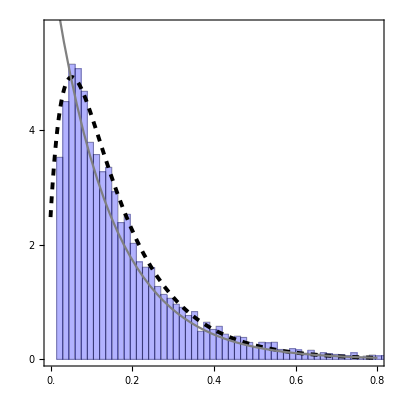

```mathematica
Show[Histogram[{GMrad21},{0.015},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[Blue,Opacity[0.3],EdgeForm[Black]]},PlotRange->{{0,0.8},{0,5.8}},FrameTicks->{{Range[0,7,2],None},(*left,right*){Range[0,0.8,0.2],None}        (*bottom,top*)}],Plot[{modelRad/.lp->0.431/.α->1.2/.γ->3.1/.γo->4/.Ai->2.48/.x->xi,1/0.144*Exp[-xi/0.144]},{xi,0,0.8},PlotStyle->{Directive[Black,Dashed,Thickness[0.007]],Directive[RGBColor[0.5,0.5,0.5],Thickness[0.004]]}]]
```

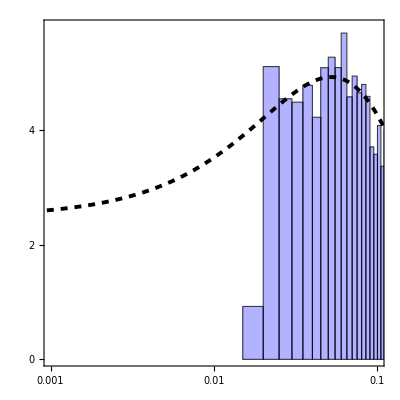

```mathematica
Show[Histogram[{GMrad21},{0.005},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[24],ChartStyle->{Directive[Blue,Opacity[0.3],EdgeForm[Black]]},PlotRange->{{0.001,0.1},{0,5.8}},FrameTicks->{{Range[0,7,2],None},(*left,right*){{0.01,0.1},None}        (*bottom,top*)},ScalingFunctions->{"Log",None}],Plot[{modelRad/.lp->0.431/.α->1.2/.γ->3.1/.γo->4/.Ai->2.48/.x->xi(*,1/144*Exp[-xi/144]*)},{xi,0,0.800},PlotStyle->{Directive[Black,Dashed,Thickness[0.007]](*,Directive[Black,Dashed,Thickness[0.007]]*)},ScalingFunctions->{"Log",None}]]
```

## Fig HiChip

```mathematica
data=Import["C:\\Users\\kitte\\Downloads\\contacts_3_both_extended.csv","Data"];
```

```mathematica
header=First[data];
rows=Rest[data];

(*Находим столбец с длиной в kb*)
lengthColumn=First@FirstPosition[header,"interaction_length"];

(*Получаем одномерный список чисел*)
ctcfHiChipKb=DeleteMissing[Quiet[Check[N@ToExpression@ToString[#],Missing["NotNumeric"]]&/@rows[[All,lengthColumn]]]]/10^6;
```

```mathematica
Length[ctcfHiChipKb]
```

21562

```mathematica
ctcfHiChipKbCrop=Table[If[And[ctcfHiChipKb[[i]]>0.001,ctcfHiChipKb[[i]]<0.800 ],ctcfHiChipKb[[i]],Nothing],{i,1,Length[ctcfHiChipKb]}];
```

```mathematica
ctcfHiChipKbCrop2=Table[If[And[ctcfHiChipKb[[i]]>1,ctcfHiChipKb[[i]]<10 ],ctcfHiChipKb[[i]],Nothing],{i,1,Length[ctcfHiChipKb]}];
```

```mathematica
data=Flatten[ctcfHiChipKbCrop2];

bins=Join[Range[1,10,1]];

counts=BinCounts[data,{bins}];

widths=Differences[bins];
centers=MovingAverage[bins,2];

heights=counts/(Total[counts] widths);

histPoints=Transpose[{centers,heights}];

(*убираем пустые бины*)
histPointsFit=Select[histPoints,#[[2]]>0&];
```

```mathematica
histPointsFit
```

{{3/2,2/7},{5/2,1/7},{7/2,23/280},{9/2,3/28},{11/2,11/140},{13/2,3/40},{15/2,5/56},{17/2,1/20},{19/2,5/56}}

```mathematica
fitExp=FindFit[histPointsFit,Am*Exp[-x/l],{{Am,0.003},{l,1}},x];

fitExp["BestFitParameters"]
```

{Am→1.14448,l→1.55182}[BestFitParameters]

```mathematica
Clear[lp]
```

```mathematica
modelCTCF/. Ai->0.018/. lp->431/. α->1.2/.γ->3.1/. γo->4/. x->xi
```

-2.77267×10^-10 ⅇ^(-0.00744734 xi) (-3.56656×10^7+4.14294×10^7 ⅇ^(-0.0189051 xi)-5.76376×10^6 ⅇ^(-0.0129085 xi))

```mathematica
bins=Join[Range[0.001,0.01,0.001],Range[0.02,0.8,0.01]];
```

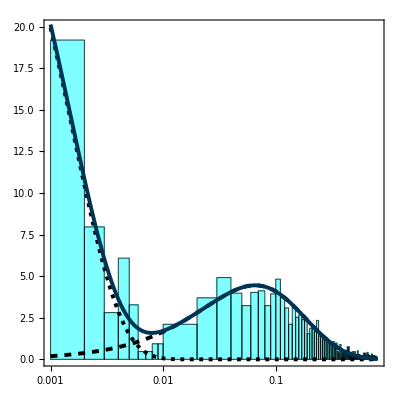

```mathematica
Show[Histogram[Flatten[ctcfHiChipKbCrop],{bins},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[RGBColor[0,1,1],Opacity[0.5]]},PlotRange->{{0.001,0.8},{0,20}},FrameTicks->{{All,None},{{0.01,0.1,0.5},None}},ScalingFunctions->{"Log",None}],Plot[{Evaluate[modelCTCF/. Ai->18/. lp->0.431/. α->1.2/.
γ->3.1/. γo->4/. x->xi],Exp[-xi/0.00155]*38,Evaluate[modelCTCF/. Ai->18/. lp->0.431/. α->1.2/.
γ->3.1/. γo->4/. x->xi]+Exp[-xi/0.00155]*38},{xi,0.001,0.8},PlotRange->All,PlotStyle->{Directive[Black,Dashed,Thickness[0.007]],Directive[Black,Dashing[{0.007,0.01}],Thickness[0.007]],Directive[RGBColor[0.,0.2,0.33],Thickness[0.007]]},ScalingFunctions->{"Log",None}]]
```

## Fig 2 ab

```mathematica
γmax=15;
γstep=3;
```

```mathematica
legend=DensityPlot[y,{x,0,1},{y,0,1},AspectRatio->10,FrameTicks->{{None,Table[{γ/γmax,γ},{γ,0,γmax,5}]},{None,None}},ColorFunction->"DarkRainbow",FrameLabel->{None,None,Style["γ"],None},FrameStyle->Directive[18,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[18,FontFamily->"CMU Serif",Black],RotateLabel->False,ImageSize->44,PlotRangePadding->None];
```

```mathematica
data=(Import["C:\\петли\\численное моделирование\\результаты\\ones.csv","CSV"][[2;;]])[[All,2]];
```

```mathematica
data1s=(Import["C:\\петли\\численное моделирование\\результаты\\archive-2026-03-25_21-36-47\\archive\\ones.csv","CSV"][[1;;]])[[All,2]];
```

```mathematica
FSize=20;
FTicksSize=16;
```

```mathematica
g1=Show[Histogram[data1s,100,"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0.1,10}},FrameLabel->{{None,None},{None,None}}],
Plot[((1+2.6/2+γo))*Exp[-x*(1+2.6/2+γo)]/.{γo->1.8},{x,0,1},PlotRange->{0,20},Frame->True,PlotStyle->{Dashing[Small],Blue,Thickness[0.015]},AspectRatio->1],Plot[Evaluate[Table[(1+γ/2+γo)*Exp[-x*(1+γ/2+γo)]/.{γo->1.8},{γ,0,γmax,γstep}]],{x,0,1},PlotRange->{0,20},Frame->True,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][1-γo/γmax]],{γo,0,γmax,γstep}],AspectRatio->1],ImageSize->250];
```

```mathematica
gammaC=(γi+(Sqrt[8*γi+(2(1+2γo)+γi)^2]-(2(1+2γo)+γi))/2)/.γo->1.8/.γi->2.7;
```

```mathematica
g2=Show[Histogram[data,100,"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5]],ChartBaseStyle->EdgeForm[Gray],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0,1},{0,5}},
FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[Table[A/.γ->(γi+(Sqrt[8*γi+(2(1+2γo)+γi)^2]-(2(1+2γo)+γi))/2)/.γo->1.8/.α->0,{γi,0,γmax,γstep}]],{x,0,1},PlotRange->{0,6},Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][1-γ/γmax]],{γ,0,γmax,γstep}],AspectRatio->1],
Plot[A/.{γo->1.8,γ->gammaC,α->0},{x,0,3},PlotRange->{0,6},Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],PlotStyle->{Dashing[Small],Blue,Thickness[0.015]}],
Plot[13.5^2*x*Exp[-x*13.5],{x,0,3},PlotStyle->Directive[RGBColor[0.5,0,0],Dashed],PlotRange->All],ImageSize->250];
```

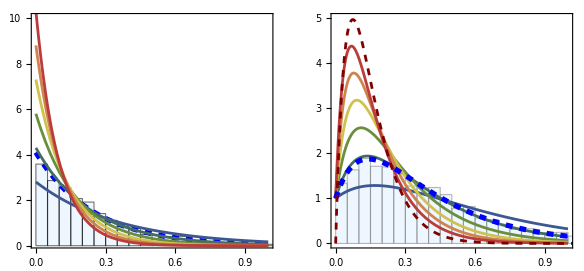

```mathematica
GraphicsRow[{g1,g2,legend}]
```

```mathematica
legend
```

-Graphics-

# Unified fitting of ChIA-PET and HiChIP loop-length distributions

```mathematica
(* modelRad and modelCTCF must be defined before this code is run.
   Expected model symbols: x, Ai, α, γ, γo, lp. *)

(* ------------------------------------------------------------------ *)
(* 1. Input files and dataset settings                                 *)
(* ------------------------------------------------------------------ *)

baseDir = NotebookDirectory[];

(* Output directory of chia_pet_unified_pipeline_no_pet_filter.py *)
chiaPetDir = "C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\chia_pet_results\\loop_length";

(* The separate HiChIP table *)
hiChipFile = FileNameJoin[{baseDir, "hichip_results", "CTCF_HICHIP.csv"}];

binKb = 10.;

ClearAll[findOne];

findOne::files = "Pattern `1` matched `2` files: `3`.";

findOne[directory_, pattern_] := Module[
  {files = FileNames[pattern, directory]},

  If[Length[files] != 1,
    Message[findOne::files, pattern, Length[files], files];
    Abort[]
  ];

  First[files]
];

(* These are the six combined PET-expanded files generated by Python.
   The *.csv* suffix accepts both .csv and .csv.gz. *)
chiaPetFiles = <|
  "RadK562" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\K562rad21.csv",

  "RadGM" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\GMrad21.csv",

  "CTCFK562" -> "C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\k562LoopLengthsCTCF.csv",

  "CTCFGM" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\gm12878LoopLengthsCTCF.csv",

  "CTCFHeLa" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\helaLoopLengthsCTCF.csv",

  "CTCFMCF7" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\mcf7LoopLengthsCTCF.csv"
|>;

If[!FileExistsQ[hiChipFile],
  Print["HiChIP file was not found: ", hiChipFile];
  Abort[]
];

(* The order is intentional:
   columns 5-11  = fitted amplitudes;
   columns 12-18 = RMSE, matching the previous tbls structure;
   columns 19-25 = nRMSE. *)
datasetOrder = {
  "RadK562",
  "RadGM",
  "CTCFK562Hi",
  "CTCFK562",
  "CTCFGM",
  "CTCFHeLa",
  "CTCFMCF7"
};

specs = <|
  "RadK562" -> <|
    "File" -> chiaPetFiles["RadK562"],
    "Column" -> "loop_length_kb",
    "Model" -> modelRad,
    "MinKb" -> 30.,
    "MaxKb" -> 800.,
    "XScale" -> 1.,
    "LpScale" -> 1.,
    "A0" -> 0.003
  |>,

  "RadGM" -> <|
    "File" -> chiaPetFiles["RadGM"],
    "Column" -> "loop_length_kb",
    "Model" -> modelRad,
    "MinKb" -> 30,
    "MaxKb" -> 800.,
    "XScale" -> 1.,
    "LpScale" -> 1.,
    "A0" -> 0.003
  |>,

  "CTCFK562Hi" -> <|
    "File" -> hiChipFile,
    "Column" -> "interaction_length_kb",
    "Model" -> modelCTCF,
    "MinKb" -> 30.,              (* remove HiChIP short-range contacts *)
    "MaxKb" -> 600.,
    "XScale" -> 1.,        (* kb -> Mb *)
    "LpScale" -> 1.,       (* lp grid is in kb; model uses Mb *)
    "A0" -> 3.
  |>,

  "CTCFK562" -> <|
    "File" -> chiaPetFiles["CTCFK562"],
    "Column" -> "loop_length_kb",
    "Model" -> modelCTCF,
    "MinKb" -> 10.,
    "MaxKb" -> 600.,
    "XScale" -> 1.,        (* kb -> Mb *)
    "LpScale" -> 1.,  
    "A0" -> 3.
  |>,

  "CTCFGM" -> <|
    "File" -> chiaPetFiles["CTCFGM"],
    "Column" -> "loop_length_kb",
    "Model" -> modelCTCF,
    "MinKb" -> 10.,
    "MaxKb" -> 600.,
    "XScale" -> 1.,        (* kb -> Mb *)
    "LpScale" -> 1.,  
    "A0" -> 3.
  |>,

  "CTCFHeLa" -> <|
    "File" -> chiaPetFiles["CTCFHeLa"],
    "Column" -> "loop_length_kb",
    "Model" -> modelCTCF,
    "MinKb" -> 10.,
    "MaxKb" -> 600.,
    "XScale" -> 1.,        (* kb -> Mb *)
    "LpScale" -> 1.,  
    "A0" -> 3.
  |>,

  "CTCFMCF7" -> <|
    "File" -> chiaPetFiles["CTCFMCF7"],
    "Column" -> "loop_length_kb",
    "Model" -> modelCTCF,
    "MinKb" -> 10.,
    "MaxKb" -> 600.,
    "XScale" -> 1.,        (* kb -> Mb *)
    "LpScale" -> 1.,  
    "A0" -> 3.
  |>
|>;
```

```mathematica
(* ------------------------------------------------------------------ *)
(* 2. Import and construction of uniformly binned PDFs                 *)
(* ------------------------------------------------------------------ *)

ClearAll[importCSV, toNumber, readNumericColumn, makePDFData];

(* Import works directly for ordinary CSV. For .csv.gz, Mathematica usually
   detects compression automatically; the fallback explicitly decompresses
   the file and parses the resulting CSV string. *)
importCSV[file_] := Quiet @ Check[
  Import[file, "CSV"],
  ImportString[Import[file, "String"], "CSV"]
];

toNumber[value_] := Quiet @ Check[
  N @ If[NumberQ[value], value, ToExpression @ ToString[value]],
  Missing["NotNumeric"]
];

readNumericColumn[file_, column_] := Module[
  {table, header, position, values},

  table = importCSV[file];
  header = First[table];
  position = FirstPosition[header, column, Missing["NotFound"]];

  If[MissingQ[position],
    Print["Column \"", column, "\" was not found in ", file];
    Abort[]
  ];

  values = toNumber /@ Rest[table][[All, First[position]]];
  Select[DeleteMissing[values], NumericQ]
];

makePDFData[spec_] := Module[
  {values, edges, density, scale},

  values = readNumericColumn[spec["File"], spec["Column"]];

  (* Filtering is performed before HistogramList, so the retained
     distribution is normalized again. For HiChIP this removes <30 kb. *)
  values = Select[
    values,
    spec["MinKb"] <= # <= spec["MaxKb"] &
  ];

  If[values === {},
    Print["No observations remain for ", spec["File"]];
    Abort[]
  ];

  {edges, density} = HistogramList[
    values,
    {spec["MinKb"], spec["MaxKb"], binKb},
    "PDF"
  ];

  scale = spec["XScale"];

  (* If x is converted from kb to Mb, density is converted from
     probability/kb to probability/Mb to preserve unit integral. *)
  Transpose[{
    MovingAverage[edges, 2] scale,
    density/scale
  }]
];

fitData = AssociationMap[makePDFData[specs[#]] &, datasetOrder];
```

```mathematica
(* ------------------------------------------------------------------ *)
(* 3. Fit one dataset at one parameter-grid point                      *)
(* ------------------------------------------------------------------ *)

ClearAll[fitOne];

fitOne[name_, {lpValue_, gammaValue_, gamma0Value_, alphaValue_}] :=
 Module[
  {spec, data, model, fit, observed, predicted, rmse, nrmse},

  spec = specs[name];
  data = fitData[name];

  model = spec["Model"] /. {
      α -> alphaValue,
      γ -> gammaValue,
      γo -> gamma0Value,
      lp -> lpValue spec["LpScale"]
    };

  fit = Quiet @ Check[
    FindFit[data, model, {{Ai, spec["A0"]}}, x],
    $Failed
  ];

  If[fit === $Failed,
    Return[{Indeterminate, Infinity, Infinity}]
  ];

  observed = data[[All, 2]];
  predicted = N[(model /. fit /. x -> #)] & /@ data[[All, 1]];

  rmse =  Mean[Abs[(observed - predicted)]];
  nrmse = rmse/Mean[observed];

  {Ai /. fit, rmse, nrmse}
];
```

```mathematica
datasetOrder
```

{RadK562,RadGM,CTCFK562Hi,CTCFK562,CTCFGM,CTCFHeLa,CTCFMCF7}

```mathematica
(* ------------------------------------------------------------------ *)
(* 4. Parameter grid and complete fit table                            *)
(* ------------------------------------------------------------------ *)

lpGrid = Range[431, 431, 50];
gammaGrid = N @ Range[0.1, 10, 0.3];
gamma0Grid =N @ Range[0.1, 10, 0.3];
alphaGrid = N @ Range[1.2,1.2, 0.2];

parameterGrid = Tuples[{
  lpGrid,
  gammaGrid,
  gamma0Grid,
  alphaGrid
}];

ClearAll[fitRow];

fitRow[parameters_] := Module[{results},
  results = fitOne[#, parameters] & /@ datasetOrder;

  Join[
    parameters,
    results[[All, 1]],     (* amplitudes *)
    results[[All, 2]],     (* RMSE *)
    results[[All, 3]]      (* nRMSE *)
  ]
];

progress = 0;

tbls = Monitor[
  Map[
    Function[parameters,
      progress++;
      fitRow[parameters]
    ],
    parameterGrid
  ],
  Row[{"Fitted parameter sets: ", progress, "/", Length[parameterGrid]}]
]
```

```mathematica
(* ------------------------------------------------------------------ *)
(* 5. Column names and export                                          *)
(* ------------------------------------------------------------------ *)

Export[
  FileNameJoin[{baseDir, "all_loop_distribution_fits.csv"}],  "CSV"
];
```

```mathematica
(* ------------------------------------------------------------------ *)
(* 6. Useful views                                                     *)
(* ------------------------------------------------------------------ *)

(* Previous RMSE indices remain unchanged:
   12,19 RadK562
   13,20 RadGM
   14,21 CTCFK562Hi
   15,22 CTCFK562
   16,23 CTCFGM
   17,24 CTCFHeLa
   18,25 CTCFMCF7

   nRMSE values occupy columns 19-25 in the same order. *)

(* Example: inspect the prepared HiChIP distribution.
   Its first x value should be close to 0.035 Mb for 10-kb bins. *)
fitData["CTCFK562Hi"] // Take[#, UpTo[5]] &
```

{{35.,0.00452333},{45.,0.00458964},{55.,0.00452957},{65.,0.00460368},{75.,0.00437666}}

```mathematica
tblsHeLa=Table[{tbls[[i,2]],tbls[[i,3]]/(1+1.2),(tbls[[i,24]])},{i,1,Length[tbls]}];
```

```mathematica
gammaC=Around[3.1,0.8](*gamma of cohesins + dynamic correction*);
gammaB=Around[1.8,0.6];
```

```mathematica
levelsHela=Range[Min[tblsHeLa[[All,3]]],0.8,0.03];
zrangeHela={Min[levelsHela],Max[levelsHela]};
```

```mathematica
legendHela=ContourPlot[y,{γ,0,2},{y,zrangeHela[[1]],zrangeHela[[2]]},FrameLabel->{None,None,None,None},
FrameStyle->Directive[18,FontFamily->"CMU Serif",Black],AxesOrigin->{0,0},Frame->True,AspectRatio->20,Contours->levelsHela,ContourShading->True,PlotRange->zrangeHela,PlotLegends->None,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,FrameTicks->{{None,Table[{γ,γ},{γ,0,1,0.1}]},{None,None}},FrameTicksStyle->Directive[14,FontFamily->"CMU Serif",Black],ImageSize->45.5,PlotRangePadding->None];
```

```mathematica
gHela=Show[ListContourPlot[tblsHeLa,Frame->True,PlotRange->{zrangeHela[[1]],zrangeHela[[2]]},Contours->levelsHela,FrameStyle->Directive[18,FontFamily->"CMU Serif",Black],ColorFunction->"TemperatureMap"],Graphics[{RGBColor[1,0,1],Opacity[0.3],Disk[{gammaC["Value"],gammaB["Value"]},{gammaC["Error"],gammaB["Error"]}]}],Graphics[Line[{{{gammaC["Value"]-0.08,gammaB["Value"]-0.04},{gammaC["Value"]+0.08,gammaB["Value"]+0.04}},{{gammaC["Value"]-0.08,gammaB["Value"]+0.04},{gammaC["Value"]+0.08,gammaB["Value"]-0.04}}}]],ImageSize->300];
```

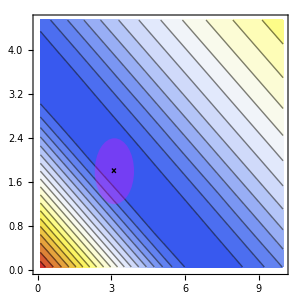

```mathematica
GraphicsRow[{gHela,legendHela}]
```

```mathematica
tblsGM=Table[{tbls[[i,2]],tbls[[i,3]]/(1+1.2),(tbls[[i,20]]+tbls[[i,23]])/2},{i,1,Length[tbls]}];
```

```mathematica
levelsGM=Range[Min[tblsGM[[All,3]]],0.8,0.03];
zrangeGM={Min[levelsGM],Max[levelsGM]};
```

```mathematica
zrangeGM[[2]]
```

0.777922

```mathematica
legendGM=ContourPlot[y,{γ,0,2},{y,zrangeGM[[1]],zrangeGM[[2]]},FrameLabel->{None,None,None,None},
FrameStyle->Directive[18,FontFamily->"CMU Serif",Black],AxesOrigin->{0,0},Frame->True,AspectRatio->20,Contours->levelsGM,ContourShading->True,PlotLegends->None,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,FrameTicks->{{None,Table[{γ,γ},{γ,Round[zrangeGM[[1]],0.1],zrangeGM[[2]],0.1}]},{None,None}},FrameTicksStyle->Directive[14,FontFamily->"CMU Serif",Black],ImageSize->45.5,PlotRangePadding->None];
```

```mathematica
gGM=Show[ListContourPlot[tblsGM,Frame->True,PlotRange->{zrangeGM[[1]],zrangeGM[[2]]},Contours->levelsGM,FrameStyle->Directive[18,FontFamily->"CMU Serif",Black],ColorFunction->"TemperatureMap"],Graphics[{RGBColor[1,0,1],Opacity[0.3],Disk[{gammaC["Value"],gammaB["Value"]},{gammaC["Error"],gammaB["Error"]}]}],Graphics[Line[{{{gammaC["Value"]-0.08,gammaB["Value"]-0.04},{gammaC["Value"]+0.08,gammaB["Value"]+0.04}},{{gammaC["Value"]-0.08,gammaB["Value"]+0.04},{gammaC["Value"]+0.08,gammaB["Value"]-0.04}}}]],ImageSize->300];
```

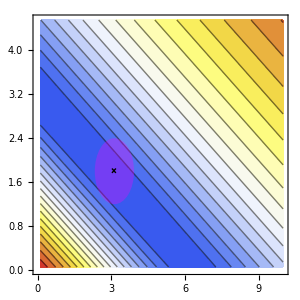

```mathematica
GraphicsRow[{gGM,legendGM}]
```

```mathematica
tblsK562=Table[{tbls[[i,2]],tbls[[i,3]]/(1+1.2),(tbls[[i,21]]+tbls[[i,22]])/2},{i,1,Length[tbls]}];
```

```mathematica
levelsK562=Range[Min[tblsK562[[All,3]]],0.8,0.03];
zrangeK562={Min[levelsK562],Max[levelsK562]};
```

```mathematica
zrangeK562
```

{0.0936284,0.783628}

```mathematica
legendK562=ContourPlot[y,{γ,0,2},{y,zrangeK562[[1]],zrangeK562[[2]]},FrameLabel->{None,None,None,None},
FrameStyle->Directive[18,FontFamily->"CMU Serif",Black],AxesOrigin->{0,0},Frame->True,AspectRatio->20,Contours->levelsK562,ContourShading->True,PlotLegends->None,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,FrameTicks->{{None,Table[{γ,γ},{γ,0,1,0.1}]},{None,None}},FrameTicksStyle->Directive[14,FontFamily->"CMU Serif",Black],ImageSize->45.5,PlotRangePadding->None];
```

```mathematica
gK562=Show[ListContourPlot[tblsK562,Frame->True,PlotRange->{zrangeK562[[1]],zrangeK562[[2]]},Contours->levelsGM,FrameStyle->Directive[18,FontFamily->"CMU Serif",Black],ColorFunction->"TemperatureMap"],Graphics[{RGBColor[1,0,1],Opacity[0.3],Disk[{gammaC["Value"],gammaB["Value"]},{gammaC["Error"],gammaB["Error"]}]}],Graphics[Line[{{{gammaC["Value"]-0.08,gammaB["Value"]-0.04},{gammaC["Value"]+0.08,gammaB["Value"]+0.04}},{{gammaC["Value"]-0.08,gammaB["Value"]+0.04},{gammaC["Value"]+0.08,gammaB["Value"]-0.04}}}]],ImageSize->300];
```

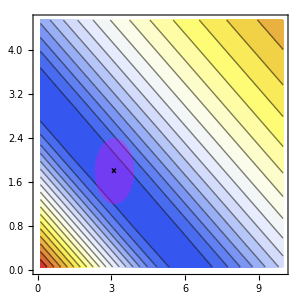

```mathematica
GraphicsRow[{gK562,legendK562}]
```